```mathematica
ResourceFunction["DarkMode"][]
```

The following function generates the ‘empty’ grid with only the boundary cells filled in. Internal cells carry the value -1.

```mathematica
initialGridBorder[n_] := initialGridBorder[n] = Normal[SparseArray[{{i_, j_} /; i == 1 || j == 1 -> i + j - 2, {i_, j_} /; i == n || j == n -> 2n - i - j}, {n, n}, -1]]
```

The following shows an example of a 9 x 9 boundary grid:

Drag the slider to see larger grids.

```mathematica
colourRules={0->Red,1->Yellow,2->Blue};
Manipulate[ArrayPlot[initialGridBorder[3(2k - 1)]],{k,1,20,1}]
```

The following codeblock contains functions that will be evaluated either at the beginning or at the end of the simulation. They generate min/max height grids, and go between 3-coloured grids to height grids.

```mathematica
(* Helper function for generateMaxHeightGrid. Fills one concentric square of cells. *)
fillConcentricSquareMax[Hold[grid_], k_] := (
 grid[[k, k ;; -k]] = grid[[k - 1, k ;; -k]] + 1; 
 grid[[-k, k ;; -k]] = grid[[-(k - 1), k ;; -k]] + 1;
 grid[[k ;; -k, k]] = grid[[k ;; -k, k - 1]] + 1; 
 grid[[k ;; -k, -k]] = grid[[k ;; -k, -(k - 1)]] + 1; 
ReleaseHold[Hold[grid]])

(* Helper function for generateMinHeightGrid. Fills one concentric square of cells. *)
fillConcentricSquareMin[Hold[grid_], k_] := (
 grid[[k, k ;; -k]] = grid[[k - 1, k ;; -k]] - 1; 
 grid[[-k, k ;; -k]] = grid[[-(k - 1), k ;; -k]] - 1;
 grid[[k ;; -k, k]] = grid[[k ;; -k, k - 1]] - 1; 
 grid[[k ;; -k, -k]] = grid[[k ;; -k, -(k - 1)]] - 1; 
ReleaseHold[Hold[grid]])

(* Generates the grid with maximum height by starting from the boundary and moving inwards, filling in concentric squares. *)
generateMaxHeightGrid[dim_] := generateMaxHeightGrid[dim] = Module[{k = 1, depth = (dim + 1) / 2},
 Nest[( k++; currGrid = #; fillConcentricSquareMax[Hold[currGrid], k]; initialGrid = currGrid ) &, initialGrid = initialGridBorder[dim], depth - 1];
 Normal[initialGrid]
]

(* Generates the grid with minimum height by starting from the boundary and moving inwards, filling in concentric squares. *)
generateMinHeightGrid[dim_] := generateMinHeightGrid[dim] = Module[{k = 1, depth = (dim + 1) / 2},
 Nest[( k++; currGrid = #; fillConcentricSquareMin[Hold[currGrid], k]; initialGrid = currGrid ) &, initialGrid = initialGridBorder[dim], depth - 1];
 Normal[initialGrid]
]

(* Takes a grid with a filled in height function as input and converts it to its corresponding 3-colouring form. *)
to3Colouring[grid_] := Mod[grid, 3]

(* Helper function for toHeightFunction *)
findListHeight[first_, list_, len_] := Module[{initialList = SparseArray[{}, {len}, -1], k = 0, prev = first}, (* remember that list is of length (len + 1) *)
 Nest[(k++; newList = #; prev = If[MemberQ[list[[{k, k + 1}]], 1], prev + list[[k + 1]] - list[[k]], If[list[[k]] == 2, prev + 1, prev - 1]]; newList[[k]] = prev; newList ) & , Normal[initialList], len]
]

(* Takes a 3-coloured grid as input and returns the corresponding grid labelled with its height values. *)
(* Note: this starts with the initial border grid *)
toHeightFunction[grid_, dim_] := Module[{heightGrid = initialGridBorder[dim], k = 1},
Nest[(k++; nextHeightGrid = #; nextHeightGrid[[k, 2 ;; -2]] = findListHeight[heightGrid[[k, 1]], Normal[grid[[k, 1 ;; -2]]], dim - 2]; nextHeightGrid) &, heightGrid, dim - 2] 
]
```

```mathematica
MatrixForm[toHeightFunction[to3Colouring[generateMaxHeightGrid[7]], 7]]
```

(0 | 1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 3 | 4 | 5 | 6 | 5
2 | 3 | 4 | 5 | 6 | 5 | 4
3 | 4 | 5 | 6 | 5 | 4 | 3
4 | 5 | 6 | 5 | 4 | 3 | 2
5 | 6 | 5 | 4 | 3 | 2 | 1
6 | 5 | 4 | 3 | 2 | 1 | 0)

```mathematica
$ProcessorType
```

x86-64

See the max height grids and their corresponding 3-colourings for different side lengths. Dark cells are the highest, while white cells are at height 0:

```mathematica
Manipulate[ArrayPlot[generateMaxHeightGrid[3(2k - 1)]],{k,1,10,1}]
Manipulate[ArrayPlot[Mod[generateMaxHeightGrid[3(2k - 1)], 3],  ColorFunction->"CandyColors"], {k,1,10,1}]
```

See the min height grids and their corresponding 3 - colourings for different side lengths . Dark cells are the highest, while white cells are at height 0 :

```mathematica
Manipulate[ArrayPlot[generateMinHeightGrid[3(2k - 1)]],{k,1,10,1}]
Manipulate[ArrayPlot[Mod[generateMinHeightGrid[3(2k - 1)], 3],  ColorFunction->"CandyColors"], {k,1,10,1}]
```

```mathematica
selectRandomCell[dim_] := RandomChoice[Tuples[Range[2, dim - 1], 2]];
coinFlip[] := RandomChoice[{True, False}]
changeColour[grid_, pos_, newVal_] := ReplacePart[grid, pos -> newVal]

(* Check if you can pop up a cell at pos in grid. Works on both height values and 3-colourings *)
checkPopUp[grid_, pos_] := AllTrue[grid[[pos[[1]] + {-1, 1}, pos[[2]]]] ~ Join ~ grid[[pos[[1]], pos[[2]] + {-1, 1}]], Mod[grid[[Sequence @@ pos]] - #, 3] == 2 &]
(* Check if you can pop down a cell at pos in grid. Works on both height values and 3-colourings *)
checkPopDown[grid_, pos_] := AllTrue[grid[[pos[[1]] + {-1, 1}, pos[[2]]]] ~ Join ~ grid[[pos[[1]], pos[[2]] + {-1, 1}]], Mod[grid[[Sequence @@ pos]] - #, 3] == 1 &]

(* If heads, check if site can be popped up; otherwise, check if site can be popped down. *)
coinFunctionAssociation = Association[True -> checkPopUp, False -> checkPopDown];
coinSignAssociation = Association[checkPopUp -> Plus, checkPopDown -> Subtract];

(* 1 Maintain a list of random coin flips in the form of a list checkPopUp, checkPopDown functions (instead of storing heads and tails) *)
(* 2 Maintain a list of random sites *)
(* 3 Generate new coin flip, add it to the list *)
(* 4 Select random cell, add it to the list *)
extendRandomLists[dim_, numSteps_, coinTosses_, sites_] := {Nest[Prepend[#, coinFunctionAssociation[coinFlip[]]] &, coinTosses, numSteps],
	Nest[Prepend[#, selectRandomCell[dim]] &, sites, numSteps]}
(* 5 Run steps from last element added to the lists to the first element added to the lists *)
(* 6 Check if they converge. If not, go back to #3 *)

(* TODO: Edit this! *)
(* Execute one step of the Markov chain *)
(* OPTIMISATION: maybe put this in the function that performs multiple steps instead of calling it over and over? *)
 oneStep[dim_, coin_, site_, maxGrid_, minGrid_] := Module[{initialGrids = {maxGrid, minGrid}, outGrids = {maxGrid, minGrid}},
 Map[If[coin[initialGrids[[#]], site], 
 (outGrids[[#]] = changeColour[initialGrids[[#]], site, Mod[coinSignAssociation[coin][initialGrids[[#]][[Sequence @@ site]], 2], 3]];)] &, {1, 2}];
 outGrids
 ]
```

```mathematica
(* testing oneStep *)
Map[MatrixForm[#] &, oneStep[5, checkPopDown, {3,3}, generateMaxHeightGrid[5], generateMinHeightGrid[5]]]
(* conclusion: oneStep works!*)
```

{(0 | 1 | 2 | 3 | 4
1 | 2 | 3 | 4 | 3
2 | 3 | 2 | 3 | 2
3 | 4 | 3 | 2 | 1
4 | 3 | 2 | 1 | 0),(0 | 1 | 2 | 3 | 4
1 | 0 | 1 | 2 | 3
2 | 1 | 0 | 1 | 2
3 | 2 | 1 | 0 | 1
4 | 3 | 2 | 1 | 0)}

```mathematica
(* testing extendRandomLists *)
arr1 = {};
arr2 = {};
{arr1, arr2} = extendRandomLists[10, 10, arr1, arr2];
Print["first:", arr1, arr2]
{arr1, arr2} = extendRandomLists[10, 10, arr1, arr2];
Print["second:", arr1, arr2]
(* conclusion: extendedRandomLists works! *)
```

first:{checkPopDown,checkPopDown,checkPopDown,checkPopUp,checkPopDown,checkPopDown,checkPopUp,checkPopUp,checkPopDown,checkPopDown}{{3,4},{6,8},{8,4},{2,3},{8,3},{9,5},{8,9},{3,3},{2,3},{9,3}}

second:{checkPopUp,checkPopUp,checkPopDown,checkPopDown,checkPopUp,checkPopDown,checkPopUp,checkPopUp,checkPopUp,checkPopDown,checkPopDown,checkPopDown,checkPopDown,checkPopUp,checkPopDown,checkPopDown,checkPopUp,checkPopUp,checkPopDown,checkPopDown}{{9,5},{7,7},{9,2},{6,8},{5,7},{8,7},{2,3},{3,3},{8,9},{7,2},{3,4},{6,8},{8,4},{2,3},{8,3},{9,5},{8,9},{3,3},{2,3},{9,3}}

The following functions help render outputs after a specified number of steps

```mathematica
(* Executes the algorithm for a specified number of steps
   and renders it with a slider you can use to move across time to see how the grid changed *)
viewChangeSteps[n_, maxGrid_, minGrid_, steps_] := (gridsList = NestList[oneStep[n,  Sequence @@ #] &, {maxGrid, minGrid}, steps]; 
Manipulate[Grid[{{ArrayPlot[gridsList[[k]][[1]], ColorFunction->"CandyColors", Frame->True], ArrayPlot[gridsList[[k]][[2]], ColorFunction->"CandyColors", Frame->True]}}],{k,1,steps,1}])

(* Calculates the sum of absolute differences between the heights of corresponding sites in the input grids *)
checkHeightDifference[n_, maxGrid_, minGrid_] := Total[Table[Abs[maxGrid[[i, j]] - minGrid[[i, j]]], {i, 2, n - 1}, {j, 2, n - 1}], 2]

(* Executes the algorithm for a specified number of steps and displays the result *)
viewAfterSteps[n_, maxGrid_, minGrid_, steps_, logInterval_, prevStep_] := Module[{step = prevStep},
  PrintTemporary[ProgressIndicator[Dynamic[step/(steps + coinprevStep)]]]; {time, finalGrids} = AbsoluteTiming[Catch[Nest[(
  If[Mod[step, logInterval] == 0 || #[[1]] == #[[2]], (Export[StringJoin[ToString[NotebookDirectory[]], "output files/coupling_", ToString[n], "/log_", ToString[step], ".mx"], #]; 
    Print[checkHeightDifference[n, #[[1]], #[[2]]]])]; 
  If[#[[1]] == #[[2]], Throw[#]]; 
  step++; 
  oneStep[n, Sequence @@ #]) &, 
  {maxGrid, minGrid}, steps + 1]]];
  {time, step, finalGrids}
]

(* Formats time *)
displayTime[time_] := DateString[time, {"Hour", ":", "Minute", ":", "Second"}]
```

```mathematica
ListPlot3D[generateMaxHeightGrid[81]]
ListPlot3D[generateMinHeightGrid[81]]
ListPlot3D[toHeightFunction[Import[NotebookDirectory[], "output files/coupling_81/log_85402849.mx"][[1]], 81]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
dim = 15;
maxGrid = to3Colouring[generateMaxHeightGrid[dim]];
minGrid = to3Colouring[generateMinHeightGrid[dim]];
checkHeightDifference[dim, maxGrid, minGrid]
```

170

```mathematica
viewChangeSteps[dim, maxGrid, minGrid, 10000]
```

```mathematica
dim = 81;
(*grid1 = to3Colouring[generateMaxHeightGrid[dim]];
grid2 = to3Colouring[generateMinHeightGrid[dim]];*)
(* NOTE: change input and stagger! *)
{grid1, grid2} = Import[NotebookDirectory[], "output files/coupling_81/log_57000000.mx"];
{time, step, {final1, final2}} = viewAfterSteps[dim, grid1, grid2, 100000000, 1000000, 57000000];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final1, ColorRules -> colourRules, Frame->True], ArrayPlot[final2, ColorRules -> colourRules, Frame->True]}}]
```

5303

$Aborted

DateString::arg: Argument time cannot be interpreted as a date or time input or as a date string format.

DateString[time,{Hour,:,Minute,:,Second}]

step steps

ArrayPlot::mat: Argument final1 at position 1 is not a list of lists.

ArrayPlot::mat: Argument final2 at position 1 is not a list of lists.

ArrayPlot[final1,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True] | ArrayPlot[final2,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True]

```mathematica
dim = 273;
grid1 = to3Colouring[generateMaxHeightGrid[dim]];
grid2 = to3Colouring[generateMinHeightGrid[dim]];
```

```mathematica
grid1
```

```mathematica
(* NOTE: change input and stagger! *)
{time, step, {final2731max, final2732min}} = viewAfterSteps[dim, grid1, grid2, 1000000000, 10000000, 0];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final2731max, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732min, ColorRules -> colourRules, Frame->True]}}]
```

$Aborted

DateString::arg: Argument time cannot be interpreted as a date or time input or as a date string format.

DateString[time,{Hour,:,Minute,:,Second}]

step steps

ArrayPlot::mat: Argument final2731max at position 1 is not a list of lists.

ArrayPlot::mat: Argument final2732min at position 1 is not a list of lists.

ArrayPlot[final2731max,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True] | ArrayPlot[final2732min,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True]

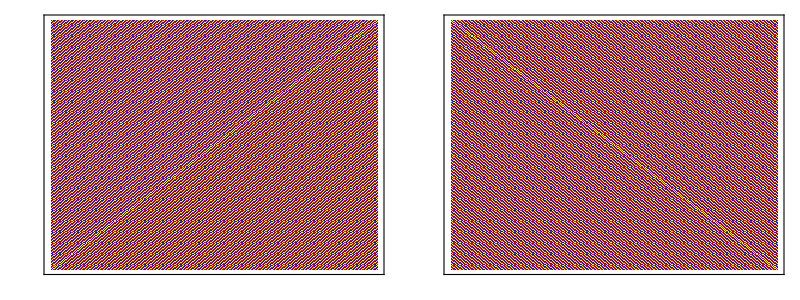

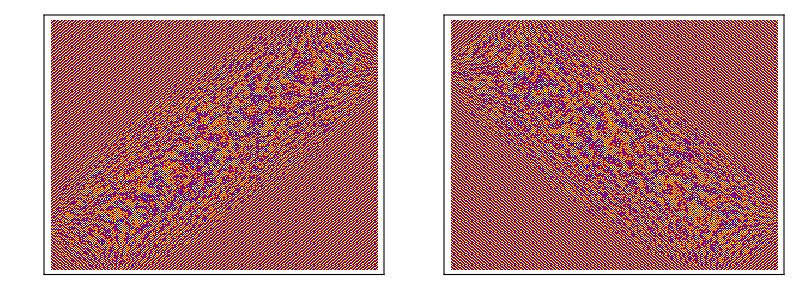

```mathematica
{initial2731, initial2732} = Import[NotebookDirectory[], "output files/coupling_273/log_0.mx"];
Grid[{{ArrayPlot[initial2731, ColorRules -> colourRules, Frame->True], ArrayPlot[initial2732, ColorRules -> colourRules, Frame->True]}}] 
{final2731, final2732} = Import[NotebookDirectory[], "output files/coupling_273/log_900000000.mx"];
Grid[{{ArrayPlot[final2731, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732, ColorRules -> colourRules, Frame->True]}}]
```

```mathematica
(* NOTE: change input and stagger! *)
{time, step, {final2731max, final2732min}} = viewAfterSteps[dim, final2731, final2732, 2000000000, 10000000, 900000000];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final2731max, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732min, ColorRules -> colourRules, Frame->True]}}]
```

$Aborted

DateString::arg: Argument time cannot be interpreted as a date or time input or as a date string format.

DateString[time,{Hour,:,Minute,:,Second}]

step steps

ArrayPlot::mat: Argument final2731max at position 1 is not a list of lists.

ArrayPlot::mat: Argument final2732min at position 1 is not a list of lists.

ArrayPlot[final2731max,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True] | ArrayPlot[final2732min,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True]

-Graphics-

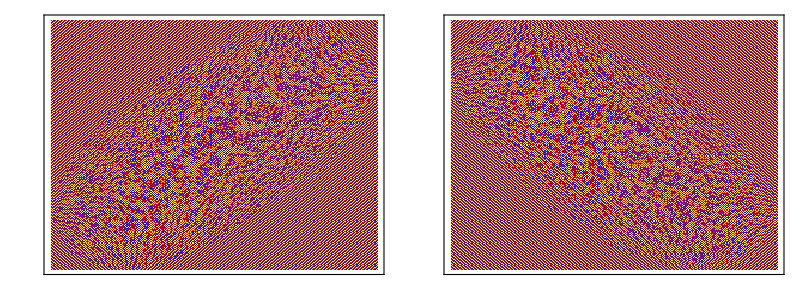

```mathematica
{initial2731, initial2732} = Import[NotebookDirectory[], "output files/coupling_273/log_0.mx"];
Grid[{{ArrayPlot[initial2731, ColorRules -> colourRules, Frame->True], ArrayPlot[initial2732, ColorRules -> colourRules, Frame->True]}}] 
{final2731, final2732} = Import[NotebookDirectory[], "output files/coupling_273/log_1400000000.mx"];
Grid[{{ArrayPlot[final2731, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732, ColorRules -> colourRules, Frame->True]}}]
```

```mathematica
(* NOTE: change input and stagger! *)
{time, step, {final2731max, final2732min}} = viewAfterSteps[dim, final2731, final2732, 2000000000, 10000000, 1400000000];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final2731max, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732min, ColorRules -> colourRules, Frame->True]}}]
```

$Aborted

DateString::arg: Argument time cannot be interpreted as a date or time input or as a date string format.

DateString[time,{Hour,:,Minute,:,Second}]

step steps

ArrayPlot::mat: Argument final2731max at position 1 is not a list of lists.

ArrayPlot::mat: Argument final2732min at position 1 is not a list of lists.

ArrayPlot[final2731max,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True] | ArrayPlot[final2732min,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True]

-Graphics-

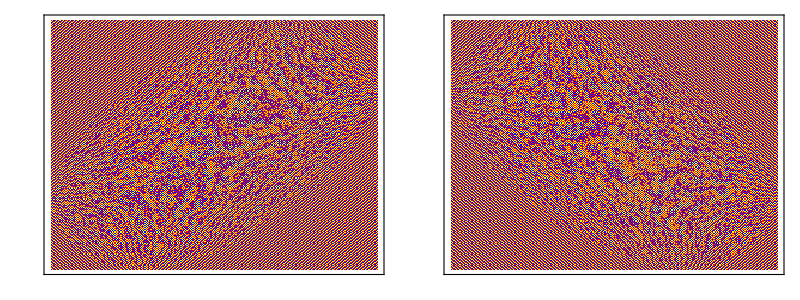

```mathematica
{initial2731, initial2732} = Import[NotebookDirectory[], "output files/coupling_273/log_0.mx"];
Grid[{{ArrayPlot[initial2731, ColorRules -> colourRules, Frame->True], ArrayPlot[initial2732, ColorRules -> colourRules, Frame->True]}}] 
{final2731, final2732} = Import[NotebookDirectory[], "output files/coupling_273/log_1950000000.mx"];
Grid[{{ArrayPlot[final2731, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732, ColorRules -> colourRules, Frame->True]}}]
```

```mathematica
(* NOTE: change input and stagger! *)
dim = 273;
{time, step, {final2731max, final2732min}} = viewAfterSteps[dim, final2731, final2732, 2000000000, 10000000, 1950000000];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final2731max, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732min, ColorRules -> colourRules, Frame->True]}}]
```

$Aborted

DateString::arg: Argument time cannot be interpreted as a date or time input or as a date string format.

DateString[time,{Hour,:,Minute,:,Second}]

step steps

ArrayPlot::mat: Argument final2731max at position 1 is not a list of lists.

ArrayPlot::mat: Argument final2732min at position 1 is not a list of lists.

ArrayPlot[final2731max,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True] | ArrayPlot[final2732min,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True]

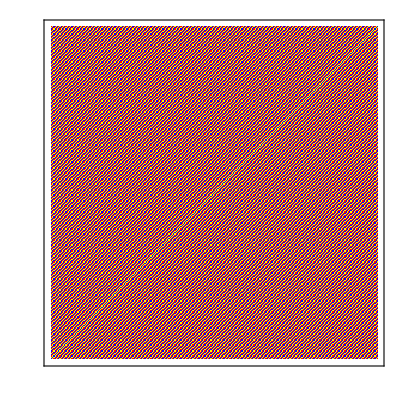
-Graphics- | -Graphics-

-Graphics- | -Graphics-

```mathematica
{initial2731, initial2732} = Import[NotebookDirectory[], "output files/coupling_273/log_0.mx"];
Grid[{{ArrayPlot[initial2731, ColorRules -> colourRules, Frame->True], ArrayPlot[initial2732, ColorRules -> colourRules, Frame->True]}}] 
{final2731, final2732} = Import[NotebookDirectory[], "output files/coupling_273/log_2660000000.mx"];
Grid[{{ArrayPlot[final2731, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732, ColorRules -> colourRules, Frame->True]}}]
```

```mathematica
(* NOTE: change input and stagger! *)
dim = 273;
{time, step, {final2731max, final2732min}} = viewAfterSteps[dim, final2731, final2732, 2000000000, 10000000, 2660000000];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final2731max, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732min, ColorRules -> colourRules, Frame->True]}}]
```

60403

```mathematica
{initial2731, initial2732} = Import[NotebookDirectory[], "output files/coupling_273/log_0.mx"];
Grid[{{ArrayPlot[initial2731, ColorRules -> colourRules, Frame->True], ArrayPlot[initial2732, ColorRules -> colourRules, Frame->True]}}] 
{final2731, final2732} = Import[NotebookDirectory[], "output files/coupling_273/log_2800000000.mx"];
Grid[{{ArrayPlot[final2731, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732, ColorRules -> colourRules, Frame->True]}}]
```

-Graphics- | -Graphics-

-Graphics- | -Graphics-

```mathematica
(* NOTE: change input and stagger! *)
dim = 273;
{time, step, {final2731max, final2732min}} = viewAfterSteps[dim, final2731, final2732, 2000000000, 10000000, 2800000000];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final2731max, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732min, ColorRules -> colourRules, Frame->True]}}]
```

$Aborted

DateString::arg: Argument time cannot be interpreted as a date or time input or as a date string format.

DateString[time,{Hour,:,Minute,:,Second}]

step steps

ArrayPlot::mat: Argument final2731max at position 1 is not a list of lists.

ArrayPlot::mat: Argument final2732min at position 1 is not a list of lists.

ArrayPlot[final2731max,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True] | ArrayPlot[final2732min,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True]

```mathematica
{initial2731, initial2732} = Import[NotebookDirectory[], "output files/coupling_273/log_0.mx"];
Grid[{{ArrayPlot[initial2731, ColorRules -> colourRules, Frame->True], ArrayPlot[initial2732, ColorRules -> colourRules, Frame->True]}}] 
{final2731, final2732} = Import[NotebookDirectory[], "output files/coupling_273/log_3090000000.mx"];
Grid[{{ArrayPlot[final2731, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732, ColorRules -> colourRules, Frame->True]}}]
```

-Graphics- | -Graphics-

-Graphics- | -Graphics-

```mathematica
(* NOTE: change input and stagger! *)
dim = 273;
{time, step, {final2731max, final2732min}} = viewAfterSteps[dim, final2731, final2732, 2000000000, 10000000, 3090000000];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final2731max, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732min, ColorRules -> colourRules, Frame->True]}}]
```

```mathematica
dim = 273;
fileNames = FileNames["*.mx", StringJoin[NotebookDirectory[], "output files/coupling_", ToString[dim]]];
sortedFileNames = SortBy[fileNames, ToExpression@StringDrop[FileBaseName[#], 4] &];
importedArrays = Import /@ sortedFileNames;
```

```mathematica
Manipulate[
  Grid[{{ArrayPlot[importedArrays[[i]][[1]], ColorRules -> colourRules, Frame->True], 
    ArrayPlot[importedArrays[[i]][[2]], ColorRules -> colourRules, Frame->True]}, 
    {ListPlot3D[toHeightFunction[importedArrays[[i]][[1]], dim]], ListPlot3D[toHeightFunction[importedArrays[[i]][[2]], dim]]}}],
  {i, 1, Length[importedArrays], 1}
]
```

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

ArrayPlot::mat: Argument importedArrays at position 1 is not a list of lists.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

ArrayPlot::mat: Argument 267 at position 1 is not a list of lists.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[(k$16969++;nextHeightGrid=#1;nextHeightGrid⟦k$16969,2;;-2⟧=findListHeight[heightGrid$16959⟦k$16969,1⟧,Normal[importedArrays⟦k$16969,Span[«2»]⟧],dim-2];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1||j==1→-2+i+j,{i$_,j$_}/;i$==dim||j$==dim→2 dim-i$-j$},{dim,dim},-1],-2+dim].

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[(k$16969++;nextHeightGrid=#1;nextHeightGrid⟦k$16969,2;;-2⟧=findListHeight[heightGrid$16959⟦k$16969,1⟧,Normal[importedArrays⟦k$16969,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

General::stop: Further output of SparseArray::adims will be suppressed during this calculation.

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[(k$16969++;nextHeightGrid=#1;nextHeightGrid⟦k$16969,2;;-2⟧=findListHeight[heightGrid$16959⟦k$16969,1⟧,Normal[importedArrays⟦k$16969,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

General::stop: Further output of Nest::intnm will be suppressed during this calculation.

Rule::rhs: Pattern i_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,Nest[(k$16969++;nextHeightGrid=#1;nextHeightGrid⟦k$16969,Span[«2»]⟧=findListHeight[Part[«3»],Normal[«1»],Plus[«2»]];nextHeightGrid)&,SparseArray[{{«2»}/;Or[«2»]→-2.+i+j,{«2»}/;Or[«2»]→Times[«2»]+Times[«2»]+Times[«2»]},{dim,dim},-1.],-2.+dim],Charting`Private`Tag11]→Nest[(k$16969++;nextHeightGrid=#1;nextHeightGrid⟦k$16969,2;;-2⟧=findListHeight[heightGrid$16959⟦k$16969,1⟧,Normal[Part[«3»]],dim-2.];nextHeightGrid)&,SparseArray[{{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→-2.+i+j,{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

Rule::rhs: Pattern j_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,Nest[(k$16969++;nextHeightGrid=#1;nextHeightGrid⟦k$16969,Span[«2»]⟧=findListHeight[Part[«3»],Normal[«1»],Plus[«2»]];nextHeightGrid)&,SparseArray[{{«2»}/;Or[«2»]→-2.+i+j,{«2»}/;Or[«2»]→Times[«2»]+Times[«2»]+Times[«2»]},{dim,dim},-1.],-2.+dim],Charting`Private`Tag11]→Nest[(k$16969++;nextHeightGrid=#1;nextHeightGrid⟦k$16969,2;;-2⟧=findListHeight[heightGrid$16959⟦k$16969,1⟧,Normal[Part[«3»]],dim-2.];nextHeightGrid)&,SparseArray[{{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→-2.+i+j,{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

Rule::rhs: Pattern i$_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,Nest[(k$16969++;nextHeightGrid=#1;nextHeightGrid⟦k$16969,Span[«2»]⟧=findListHeight[Part[«3»],Normal[«1»],Plus[«2»]];nextHeightGrid)&,SparseArray[{{«2»}/;Or[«2»]→-2.+i+j,{«2»}/;Or[«2»]→Times[«2»]+Times[«2»]+Times[«2»]},{dim,dim},-1.],-2.+dim],Charting`Private`Tag11]→Nest[(k$16969++;nextHeightGrid=#1;nextHeightGrid⟦k$16969,2;;-2⟧=findListHeight[heightGrid$16959⟦k$16969,1⟧,Normal[Part[«3»]],dim-2.];nextHeightGrid)&,SparseArray[{{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→-2.+i+j,{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Nest[(k$16969++;nextHeightGrid=#1;nextHeightGrid⟦k$16969,2;;-2⟧=findListHeight[heightGrid$16959⟦k$16969,1⟧,Normal[importedArrays⟦k$16969,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim])

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Nest[(k$17194++;nextHeightGrid=#1;nextHeightGrid⟦k$17194,2;;-2⟧=findListHeight[heightGrid$17194⟦k$17194,1⟧,Normal[267.⟦k$17194,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim])

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Nest[(k$16969++;nextHeightGrid=#1;nextHeightGrid⟦k$16969,2;;-2⟧=findListHeight[heightGrid$16959⟦k$16969,1⟧,Normal[importedArrays⟦k$16969,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim])

General::stop: Further output of Visualization`Core`ListPlot3D::arrayerr will be suppressed during this calculation.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

ArrayPlot::mat: Argument importedArrays at position 1 is not a list of lists.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

ArrayPlot::mat: Argument 267 at position 1 is not a list of lists.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[(k$20271++;nextHeightGrid=#1;nextHeightGrid⟦k$20271,2;;-2⟧=findListHeight[heightGrid$20271⟦k$20271,1⟧,Normal[importedArrays⟦k$20271,Span[«2»]⟧],dim-2];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1||j==1→-2+i+j,{i$_,j$_}/;i$==dim||j$==dim→2 dim-i$-j$},{dim,dim},-1],-2+dim].

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[(k$20271++;nextHeightGrid=#1;nextHeightGrid⟦k$20271,2;;-2⟧=findListHeight[heightGrid$20271⟦k$20271,1⟧,Normal[importedArrays⟦k$20271,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[(k$20271++;nextHeightGrid=#1;nextHeightGrid⟦k$20271,2;;-2⟧=findListHeight[heightGrid$20271⟦k$20271,1⟧,Normal[importedArrays⟦k$20271,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

General::stop: Further output of Nest::intnm will be suppressed during this calculation.

Rule::rhs: Pattern i_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,Nest[(k$20271++;nextHeightGrid=#1;nextHeightGrid⟦k$20271,Span[«2»]⟧=findListHeight[Part[«3»],Normal[«1»],Plus[«2»]];nextHeightGrid)&,SparseArray[{{«2»}/;Or[«2»]→-2.+i+j,{«2»}/;Or[«2»]→Times[«2»]+Times[«2»]+Times[«2»]},{dim,dim},-1.],-2.+dim],Charting`Private`Tag15]→Nest[(k$20271++;nextHeightGrid=#1;«1»=«1»;nextHeightGrid)&,«1»,«1»].

Rule::rhs: Pattern j_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,Nest[(k$20271++;nextHeightGrid=#1;nextHeightGrid⟦k$20271,Span[«2»]⟧=findListHeight[Part[«3»],Normal[«1»],Plus[«2»]];nextHeightGrid)&,SparseArray[{{«2»}/;Or[«2»]→-2.+i+j,{«2»}/;Or[«2»]→Times[«2»]+Times[«2»]+Times[«2»]},{dim,dim},-1.],-2.+dim],Charting`Private`Tag15]→Nest[(k$20271++;nextHeightGrid=#1;«1»=«1»;nextHeightGrid)&,«1»,«1»].

Rule::rhs: Pattern i$_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,Nest[(k$20271++;nextHeightGrid=#1;nextHeightGrid⟦k$20271,Span[«2»]⟧=findListHeight[Part[«3»],Normal[«1»],Plus[«2»]];nextHeightGrid)&,SparseArray[{{«2»}/;Or[«2»]→-2.+i+j,{«2»}/;Or[«2»]→Times[«2»]+Times[«2»]+Times[«2»]},{dim,dim},-1.],-2.+dim],Charting`Private`Tag15]→Nest[(k$20271++;nextHeightGrid=#1;«1»=«1»;nextHeightGrid)&,«1»,«1»].

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Nest[(k$20271++;nextHeightGrid=#1;nextHeightGrid⟦k$20271,2;;-2⟧=findListHeight[heightGrid$20271⟦k$20271,1⟧,Normal[importedArrays⟦k$20271,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim])

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Nest[(k$20346++;nextHeightGrid=#1;nextHeightGrid⟦k$20346,2;;-2⟧=findListHeight[heightGrid$20346⟦k$20346,1⟧,Normal[267.⟦k$20346,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim])

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

General::stop: Further output of SparseArray::adims will be suppressed during this calculation.

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Nest[(k$20271++;nextHeightGrid=#1;nextHeightGrid⟦k$20271,2;;-2⟧=findListHeight[heightGrid$20271⟦k$20271,1⟧,Normal[importedArrays⟦k$20271,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim])

General::stop: Further output of Visualization`Core`ListPlot3D::arrayerr will be suppressed during this calculation.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

ArrayPlot::mat: Argument importedArrays at position 1 is not a list of lists.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

ArrayPlot::mat: Argument 267 at position 1 is not a list of lists.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through -2 in 2.

Part::partw: Part {3,4} of importedArrays⟦2,1;;-2⟧ does not exist.

Part::partw: Part {4,5} of importedArrays⟦2,1;;-2⟧ does not exist.

Part::partw: Part 4 of importedArrays⟦2,1;;-2⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 1 through -2 in 3.

Part::take: Cannot take positions 1 through -2 in 4.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

ArrayPlot::mat: Argument importedArrays at position 1 is not a list of lists.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

ArrayPlot::mat: Argument 267 at position 1 is not a list of lists.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through -2 in 2.

Part::partw: Part {3,4} of importedArrays⟦2,1;;-2⟧ does not exist.

Part::partw: Part {4,5} of importedArrays⟦2,1;;-2⟧ does not exist.

Part::partw: Part 4 of importedArrays⟦2,1;;-2⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 1 through -2 in 3.

Part::take: Cannot take positions 1 through -2 in 4.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

ArrayPlot::mat: Argument importedArrays at position 1 is not a list of lists.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

ArrayPlot::mat: Argument 267 at position 1 is not a list of lists.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[(k$10099++;nextHeightGrid=#1;nextHeightGrid⟦k$10099,2;;-2⟧=findListHeight[heightGrid$10079⟦k$10099,1⟧,Normal[importedArrays⟦k$10099,Span[«2»]⟧],dim-2];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1||j==1→-2+i+j,{i$_,j$_}/;i$==dim||j$==dim→2 dim-i$-j$},{dim,dim},-1],-2+dim].

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[(k$10099++;nextHeightGrid=#1;nextHeightGrid⟦k$10099,2;;-2⟧=findListHeight[heightGrid$10079⟦k$10099,1⟧,Normal[importedArrays⟦k$10099,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

General::stop: Further output of SparseArray::adims will be suppressed during this calculation.

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[(k$10099++;nextHeightGrid=#1;nextHeightGrid⟦k$10099,2;;-2⟧=findListHeight[heightGrid$10079⟦k$10099,1⟧,Normal[importedArrays⟦k$10099,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

General::stop: Further output of Nest::intnm will be suppressed during this calculation.

Rule::rhs: Pattern i_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,Nest[(k$10099++;nextHeightGrid=#1;nextHeightGrid⟦k$10099,Span[«2»]⟧=findListHeight[Part[«3»],Normal[«1»],Plus[«2»]];nextHeightGrid)&,SparseArray[{{«2»}/;Or[«2»]→-2.+i+j,{«2»}/;Or[«2»]→Times[«2»]+Times[«2»]+Times[«2»]},{dim,dim},-1.],-2.+dim],Charting`Private`Tag11]→Nest[(k$10099++;nextHeightGrid=#1;nextHeightGrid⟦k$10099,2;;-2⟧=findListHeight[heightGrid$10079⟦k$10099,1⟧,Normal[Part[«3»]],dim-2.];nextHeightGrid)&,SparseArray[{{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→-2.+i+j,{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

Rule::rhs: Pattern j_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,Nest[(k$10099++;nextHeightGrid=#1;nextHeightGrid⟦k$10099,Span[«2»]⟧=findListHeight[Part[«3»],Normal[«1»],Plus[«2»]];nextHeightGrid)&,SparseArray[{{«2»}/;Or[«2»]→-2.+i+j,{«2»}/;Or[«2»]→Times[«2»]+Times[«2»]+Times[«2»]},{dim,dim},-1.],-2.+dim],Charting`Private`Tag11]→Nest[(k$10099++;nextHeightGrid=#1;nextHeightGrid⟦k$10099,2;;-2⟧=findListHeight[heightGrid$10079⟦k$10099,1⟧,Normal[Part[«3»]],dim-2.];nextHeightGrid)&,SparseArray[{{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→-2.+i+j,{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

Rule::rhs: Pattern i$_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,Nest[(k$10099++;nextHeightGrid=#1;nextHeightGrid⟦k$10099,Span[«2»]⟧=findListHeight[Part[«3»],Normal[«1»],Plus[«2»]];nextHeightGrid)&,SparseArray[{{«2»}/;Or[«2»]→-2.+i+j,{«2»}/;Or[«2»]→Times[«2»]+Times[«2»]+Times[«2»]},{dim,dim},-1.],-2.+dim],Charting`Private`Tag11]→Nest[(k$10099++;nextHeightGrid=#1;nextHeightGrid⟦k$10099,2;;-2⟧=findListHeight[heightGrid$10079⟦k$10099,1⟧,Normal[Part[«3»]],dim-2.];nextHeightGrid)&,SparseArray[{{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→-2.+i+j,{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

ListPlot3D::arrayerr: Nest[(k$10099++;nextHeightGrid=#1;nextHeightGrid⟦k$10099,2;;-2⟧=findListHeight[heightGrid$10079⟦k$10099,1⟧,Normal[importedArrays⟦k$10099,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim] must be a valid array or a list of valid arrays.

ListPlot3D::arrayerr: Nest[(k$10417++;nextHeightGrid=#1;nextHeightGrid⟦k$10417,2;;-2⟧=findListHeight[heightGrid$10417⟦k$10417,1⟧,Normal[267.⟦k$10417,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim] must be a valid array or a list of valid arrays.

ListPlot3D::arrayerr: Nest[(k$10099++;nextHeightGrid=#1;nextHeightGrid⟦k$10099,2;;-2⟧=findListHeight[heightGrid$10079⟦k$10099,1⟧,Normal[importedArrays⟦k$10099,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPlot3D::arrayerr will be suppressed during this calculation.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

ArrayPlot::mat: Argument importedArrays at position 1 is not a list of lists.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

ArrayPlot::mat: Argument 267 at position 1 is not a list of lists.

Part::partd: Part specification importedArrays⟦267⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[(k$11197++;nextHeightGrid=#1;nextHeightGrid⟦k$11197,2;;-2⟧=findListHeight[heightGrid$11179⟦k$11197,1⟧,Normal[importedArrays⟦k$11197,Span[«2»]⟧],dim-2];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1||j==1→-2+i+j,{i$_,j$_}/;i$==dim||j$==dim→2 dim-i$-j$},{dim,dim},-1],-2+dim].

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[(k$11197++;nextHeightGrid=#1;nextHeightGrid⟦k$11197,2;;-2⟧=findListHeight[heightGrid$11179⟦k$11197,1⟧,Normal[importedArrays⟦k$11197,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

SparseArray::adims: Array dimension specification {dim,dim} should be Automatic, a non-negative machine integer, or a list of non-negative machine integers.

General::stop: Further output of SparseArray::adims will be suppressed during this calculation.

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[(k$11197++;nextHeightGrid=#1;nextHeightGrid⟦k$11197,2;;-2⟧=findListHeight[heightGrid$11179⟦k$11197,1⟧,Normal[importedArrays⟦k$11197,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

General::stop: Further output of Nest::intnm will be suppressed during this calculation.

Rule::rhs: Pattern i_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,Nest[(k$11197++;nextHeightGrid=#1;nextHeightGrid⟦k$11197,Span[«2»]⟧=findListHeight[Part[«3»],Normal[«1»],Plus[«2»]];nextHeightGrid)&,SparseArray[{{«2»}/;Or[«2»]→-2.+i+j,{«2»}/;Or[«2»]→Times[«2»]+Times[«2»]+Times[«2»]},{dim,dim},-1.],-2.+dim],Charting`Private`Tag14]→Nest[(k$11197++;nextHeightGrid=#1;nextHeightGrid⟦k$11197,2;;-2⟧=findListHeight[heightGrid$11179⟦k$11197,1⟧,Normal[Part[«3»]],dim-2.];nextHeightGrid)&,SparseArray[{{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→-2.+i+j,{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

Rule::rhs: Pattern j_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,Nest[(k$11197++;nextHeightGrid=#1;nextHeightGrid⟦k$11197,Span[«2»]⟧=findListHeight[Part[«3»],Normal[«1»],Plus[«2»]];nextHeightGrid)&,SparseArray[{{«2»}/;Or[«2»]→-2.+i+j,{«2»}/;Or[«2»]→Times[«2»]+Times[«2»]+Times[«2»]},{dim,dim},-1.],-2.+dim],Charting`Private`Tag14]→Nest[(k$11197++;nextHeightGrid=#1;nextHeightGrid⟦k$11197,2;;-2⟧=findListHeight[heightGrid$11179⟦k$11197,1⟧,Normal[Part[«3»]],dim-2.];nextHeightGrid)&,SparseArray[{{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→-2.+i+j,{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

Rule::rhs: Pattern i$_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,Nest[(k$11197++;nextHeightGrid=#1;nextHeightGrid⟦k$11197,Span[«2»]⟧=findListHeight[Part[«3»],Normal[«1»],Plus[«2»]];nextHeightGrid)&,SparseArray[{{«2»}/;Or[«2»]→-2.+i+j,{«2»}/;Or[«2»]→Times[«2»]+Times[«2»]+Times[«2»]},{dim,dim},-1.],-2.+dim],Charting`Private`Tag14]→Nest[(k$11197++;nextHeightGrid=#1;nextHeightGrid⟦k$11197,2;;-2⟧=findListHeight[heightGrid$11179⟦k$11197,1⟧,Normal[Part[«3»]],dim-2.];nextHeightGrid)&,SparseArray[{{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→-2.+i+j,{Pattern[«2»],Pattern[«2»]}/;Equal[«2»]||Equal[«2»]→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim].

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

ListPlot3D::arrayerr: Nest[(k$11197++;nextHeightGrid=#1;nextHeightGrid⟦k$11197,2;;-2⟧=findListHeight[heightGrid$11179⟦k$11197,1⟧,Normal[importedArrays⟦k$11197,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim] must be a valid array or a list of valid arrays.

ListPlot3D::arrayerr: Nest[(k$11378++;nextHeightGrid=#1;nextHeightGrid⟦k$11378,2;;-2⟧=findListHeight[heightGrid$11378⟦k$11378,1⟧,Normal[267.⟦k$11378,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim] must be a valid array or a list of valid arrays.

ListPlot3D::arrayerr: Nest[(k$11197++;nextHeightGrid=#1;nextHeightGrid⟦k$11197,2;;-2⟧=findListHeight[heightGrid$11179⟦k$11197,1⟧,Normal[importedArrays⟦k$11197,Span[«2»]⟧],dim-2.];nextHeightGrid)&,SparseArray[{{i_,j_}/;i==1.||j==1.→-2.+i+j,{i$_,j$_}/;i$==dim||j$==dim→2. dim-1. i$-1. j$},{dim,dim},-1.],-2.+dim] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPlot3D::arrayerr will be suppressed during this calculation.

```mathematica
frames = Table[Grid[{{ArrayPlot[importedArrays[[i]][[1]], ColorRules -> colourRules, Frame->True], 
    ArrayPlot[importedArrays[[i]][[2]], ColorRules -> colourRules, Frame->True]}, 
    {ListPlot3D[toHeightFunction[importedArrays[[i]][[1]], dim]], ListPlot3D[toHeightFunction[importedArrays[[i]][[2]], dim]]}}],
  {i, 1, Length[importedArrays], 1}];
```

```mathematica
Export[StringJoin[NotebookDirectory[], "coupling_81.mov"], frames, "VideoEncoding"->"MPEG1VIDEO", "FrameRate"->2]
```

/localhome/nupur23/Documents/dimer models/code/coupling_81.mov

```mathematica
dim = 25;
Grid[{{ArrayPlot[generateMaxHeightGrid[dim]], 
    ArrayPlot[generateMinHeightGrid[dim]]}, 
    {ArrayPlot[Mod[generateMaxHeightGrid[dim], 3],  ColorFunction->"CandyColors"], 
    ArrayPlot[Mod[generateMinHeightGrid[dim], 3],  ColorFunction->"CandyColors"]}}]
```

-Graphics-

```mathematica
Export[StringJoin[NotebookDirectory[], "initialGrids.pdf"], %]
```

/localhome/nupur23/Documents/dimer models/code/initialGrids.pdf

```mathematica
thisgrid = to3Colouring[generateMaxHeightGrid[273]];
```

```mathematica
ArrayPlot[thisgrid]
```

-Graphics-

```mathematica
Grid[{{ArrayPlot[thisgrid, ColorRules -> colourRules, Frame->True], ArrayPlot[to3Colouring[generateMinHeightGrid[273]], ColorRules -> colourRules, Frame->True]}}]
```

-Graphics- | -Graphics-

```mathematica
{initial5111, initial5112} = Import[NotebookDirectory[], "output files/coupling_511/log_0.mx"];
Grid[{{ArrayPlot[initial5111, ColorRules -> colourRules, Frame->True], ArrayPlot[initial5112, ColorRules -> colourRules, Frame->True]}}] 
{final5111, final5112} = Import[NotebookDirectory[], "output files/coupling_511/log_660000000.mx"];
Grid[{{ArrayPlot[final5111, ColorRules -> colourRules, Frame->True], ArrayPlot[final5112, ColorRules -> colourRules, Frame->True]}}]
```

-Graphics- | -Graphics-

-Graphics- | -Graphics-

```mathematica
{initial1, initial2} = Import[NotebookDirectory[], "output files/coupling_273/log_0.mx"];
Grid[{{ArrayPlot[initial1, ColorRules -> colourRules, Frame->True], ArrayPlot[initial2, ColorRules -> colourRules, Frame->True]}}] 
{final2731, final2732} = Import[NotebookDirectory[], "output files/coupling_273/log_930000000.mx"];
Grid[{{ArrayPlot[final2731, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732, ColorRules -> colourRules, Frame->True]}}]
```

-Graphics- | -Graphics-

-Graphics- | -Graphics-

```mathematica
dim = 511;
grid1 = to3Colouring[generateMaxHeightGrid[dim]];
grid2 = to3Colouring[generateMinHeightGrid[dim]];
(* NOTE: change input and stagger! *)
{time, step, {final5111max, final5112min}} = viewAfterSteps[dim, grid1, grid2, 1000000000, 10000000, 0];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final5111max, ColorRules -> colourRules, Frame->True], ArrayPlot[final5112min, ColorRules -> colourRules, Frame->True]}}]
```

$Aborted

00:27:20

28402849 steps

ArrayPlot::mat: Argument final5111max at position 1 is not a list of lists.

ArrayPlot::mat: Argument final5112min at position 1 is not a list of lists.

ArrayPlot[final5111max,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True] | ArrayPlot[final5112min,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True]

```mathematica
{intermediate5111, intermediate5112} = Import[NotebookDirectory[], "output files/coupling_511/log_570000000.mx"];
{time, step, {final5111max, final5112min}} = viewAfterSteps[dim, grid1, grid2, 1000000000, 10000000, 570000000];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final5111max, ColorRules -> colourRules, Frame->True], ArrayPlot[final5112min, ColorRules -> colourRules, Frame->True]}}]
```

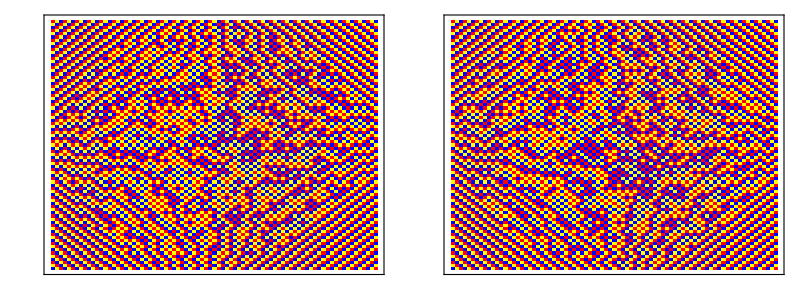

```mathematica
{final1, final2} = Import[NotebookDirectory[], "output files/coupling_81/log_57000000.mx"];
Grid[{{ArrayPlot[final1, ColorRules -> colourRules, Frame->True], ArrayPlot[final2, ColorRules -> colourRules, Frame->True]}}]
```

```mathematica
dim = 9;
minGrid = to3Colouring[generateMinHeightGrid[dim]];
oneStep[dim, maxGrid, minGrid]
(*MatrixForm[generateMaxHeightGrid[dim]]
MatrixForm[maxGrid]
MatrixForm[generateMinHeightGrid[dim]]
MatrixForm[minGrid]
coin = True; MatrixForm[to3Colouring[generateMinHeightGrid[dim]]]
site = {5,5};
Map[# = changeColour[#, site, Mod[coinSignAssociation[coin][#[[Sequence @@ site]], 2], 3]] &, {maxGrid, minGrid}]
Map[If[coinFunctionAssociation[coin][#, site], changeColour[#, site, Mod[coinSignAssociation[coin][#[[Sequence @@ site]], 2], 3]]] &, {maxGrid, minGrid}];
(*If[coinFunctionAssociation[coin][minGrid, site], minGrid = changeColour[minGrid, site, Mod[coinSignAssociation[coin][minGrid[[Sequence @@ site]], 2], 3]]]*)*)
(*MatrixForm[maxGrid]
MatrixForm[minGrid]*)
```

{{{0,1,2,0,1,2,0,1,2},{1,2,0,1,2,0,1,2,1},{2,0,1,2,0,1,2,1,0},{0,1,2,0,1,2,1,0,2},{1,2,0,1,2,1,0,2,1},{2,0,1,2,1,0,2,1,0},{0,1,2,1,0,2,1,0,2},{1,2,1,0,2,1,0,2,1},{2,1,0,2,1,0,2,1,0}},{{0,1,2,0,1,2,0,1,2},{1,0,1,2,0,1,2,0,1},{2,1,0,1,2,0,1,2,0},{0,2,1,0,1,2,0,1,2},{1,0,2,1,0,1,2,0,1},{2,1,0,2,1,0,1,2,0},{0,2,1,0,2,1,0,1,2},{1,0,2,1,0,2,1,0,1},{2,1,0,2,1,0,2,1,0}}}

(0 | 1 | 2 | 0 | 1 | 2 | 0 | 1 | 2
1 | 2 | 0 | 1 | 2 | 0 | 1 | 2 | 1
2 | 0 | 1 | 2 | 0 | 1 | 2 | 1 | 0
0 | 1 | 2 | 0 | 1 | 2 | 1 | 0 | 2
1 | 2 | 0 | 1 | 2 | 1 | 0 | 2 | 1
2 | 0 | 1 | 2 | 1 | 0 | 2 | 1 | 0
0 | 1 | 2 | 1 | 0 | 2 | 1 | 0 | 2
1 | 2 | 1 | 0 | 2 | 1 | 0 | 2 | 1
2 | 1 | 0 | 2 | 1 | 0 | 2 | 1 | 0)

(0 | 1 | 2 | 0 | 1 | 2 | 0 | 1 | 2
1 | 0 | 1 | 2 | 0 | 1 | 2 | 0 | 1
2 | 1 | 0 | 1 | 2 | 0 | 1 | 2 | 0
0 | 2 | 1 | 0 | 1 | 2 | 0 | 1 | 2
1 | 0 | 2 | 1 | 0 | 1 | 2 | 0 | 1
2 | 1 | 0 | 2 | 1 | 0 | 1 | 2 | 0
0 | 2 | 1 | 0 | 2 | 1 | 0 | 1 | 2
1 | 0 | 2 | 1 | 0 | 2 | 1 | 0 | 1
2 | 1 | 0 | 2 | 1 | 0 | 2 | 1 | 0)

```mathematica
Nest[Append[#, selectRandomCell[5]] &, {}, 5]
```

{{4,3},{4,2},{3,4},{3,4},{2,2}}